```mathematica
T0 = 1/100;
Te = 0.009;
Tp = 0.65*Te;
Ta = 0.001;
```

```mathematica
Tx[Te_,Ta_,T0_,Tp_]:= Te(1-(1/2 Te^2-Te Tp)/(2 Te^2-3Te Tp + 6 Ta (Te - Tp) DD[T0,Te,Ta]))
```

```mathematica
DD[T0_,Te_,Ta_]:=1 - ((T0-Te)/Ta)/(ⅇ^((T0-Te)/Ta)-1)
Ugd[Te_,Ta_,T0_,Tp_,KK_]:= 4 KK Te (Tp -Te) (Tx[Te,Ta,T0,Tp] - Te)
f[t_,Te_,Ta_,T0_,Tp_,KK_]:=KK t^2(t^2 - 4/3 t (Tp + Tx[Te,Ta,T0,Tp]) + 2Tp Tx[Te,Ta,T0,Tp])
g[t_,Te_,Ta_,T0_,Tp_,KK_]:= f[Te,Te,Ta,T0,Tp,KK] + Ta Ugd[Te,Ta,T0,Tp,KK] (1-ⅇ^(-(t-Te)/Ta)-((t-Te)/Ta)ⅇ^(-(T0-Te)/Ta))/(1 - ⅇ^(-(T0-Te)/Ta))
Ug [t_,Te_,Ta_,T0_,Tp_,KK_]:=Piecewise[{{f[t,Te,Ta,T0,Tp,KK],0≤t ≤ Te},{g[t,Te,Ta,T0,Tp,KK],Te ≤ t ≤ T0}}]
```

```mathematica
Manipulate[Plot[Ug[t,Te,Ta,T0,Tp,1],{t,0,2*T0}],{{T0,1/100},0,1/50},{{Te,0.009},0,0.01},{{Ta,0.001},0,1},{{Tp,0.001},0,0.01}]
```

```mathematica
Simplify[f[Tp,Te,Ta,T0,Tp,1]]
```

-1/3 Tp^3 (Tp-2 Tx[Te,Ta,T0,Tp])

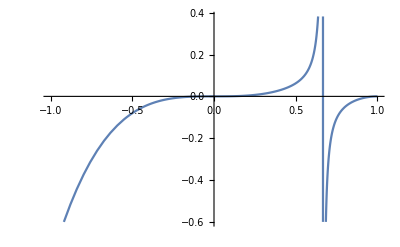

```mathematica
Plot[((1-Tp)^2 Tp^3)/(2*1-3Tp),{Tp,-1,1}]
```

```mathematica
Solve[(KK(Te-Tp)^2 Tp^3)/(2*Te-3Tp)==0,Tp]
```

{{Tp→0},{Tp→0},{Tp→0},{Tp→Te},{Tp→Te}}